```mathematica
观察x2与θ相关
```

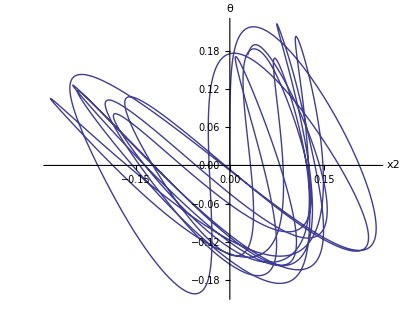

```mathematica
g=9.8;m1=0.1;m2=0.05;k=0.5;
L1=1;L2=0.2;tm=20.0;
initial1={0,0.8/L1};initial2={0,0.0,-(L1+L2),0};
P1=x2[t]^2+y2[t]^2+L1^2;
P2=2L1*(y2[t] Cos[θ[t]]-x2[t] Sin[θ[t]]);
L=√(P1+P2);
equ={
θ''[t]==
k (y2[t] Sin[θ[t]]+x2[t] Cos[θ[t]]) 
(1-L2/L) /(m1 L1)-g Sin[θ[t]]/L1,
x2''[t]==
-k (x2[t]-L1 Sin[θ[t]]) (1-L2/L)/m2,
y2''[t]==
-k (y2[t]+L1 Cos[θ[t]]) (1-L2/L)/m2-g,
θ[0]==initial1[[1]],θ'[0]==initial1[[2]],x2[0]==initial2[[1]],x2'[0]==initial2[[2]],y2[0]==initial2[[3]],y2'[0]==initial2[[4]]};
s=NDSolve[equ,{θ,x2,y2},{t,0,tm},MaxSteps->∞];
{θ,x2}={θ,x2}/.s[[1]];
ParametricPlot[{x2[t],θ[t]},{t,0,tm},
PlotPoints->1000,AxesOrigin->{0,0},
AxesLabel->{"x2","θ"}]
Clear[g,m1,m2,L1,L2,L,tm,initial1,initial2,
k,equ,s,θ,x2]
```